# Reference papers

## Perturbative Gadgets at Arbitrary Orders

## Stephen P. Jordan and Edward Farhi

```mathematica
$Assumptions=λ∈Reals;
$Assumptions=λ>0;
```

```mathematica
II := IdentityMatrix[2]
X:=PauliMatrix[1]
Y:=PauliMatrix[2]
Z := PauliMatrix[3]
```

## "All-Z" example

### By hand for n = 2

```mathematica
(*s:=(-1)^(2+1)*)
s:=1
k:=2
Hcomp:=KroneckerProduct[Z,Z]
Hgad := s((1/2)*KroneckerProduct[II, II, II, II]-(1/2)*KroneckerProduct[II, II, Z, Z]+λ*KroneckerProduct[Z, II, X, II]+λ*KroneckerProduct[II, Z, II, X])
```

```mathematica
Hgad//MatrixForm
```

(0 | λ | λ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
λ | 1 | 0 | λ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
λ | 0 | 1 | λ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | λ | λ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -λ | λ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -λ | 1 | 0 | λ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | λ | 0 | 1 | -λ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | λ | -λ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | λ | -λ | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | λ | 1 | 0 | -λ | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -λ | 0 | 1 | λ | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -λ | λ | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -λ | -λ | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -λ | 1 | 0 | -λ
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -λ | 0 | 1 | -λ
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -λ | -λ | 0)

```mathematica
Eigenvalues[Hgad]
```

{1,1,1,1,0,0,0,0,1/2 (1-√(1+16 λ^2)),1/2 (1-√(1+16 λ^2)),1/2 (1-√(1+16 λ^2)),1/2 (1-√(1+16 λ^2)),1/2 (1+√(1+16 λ^2)),1/2 (1+√(1+16 λ^2)),1/2 (1+√(1+16 λ^2)),1/2 (1+√(1+16 λ^2))}

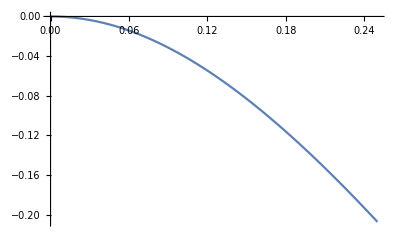

```mathematica
Plot[1/2 (1-√(1+16 λ^2)),{λ,0,0.25}]
```

```mathematica
Eigenvectors[Hgad][[9]]
```

{0,0,0,0,0,0,0,0,0,0,0,0,1,-(1-√(1+16 λ^2))/(4 λ),-(1-√(1+16 λ^2))/(4 λ),1}

```mathematica
Norm[Eigenvectors[Hgad][[9]]]
```

√(2+1/8 Abs[(1-√(1+16 λ^2))/λ]^2)

```mathematica
Hgad00:=(1/2)*KroneckerProduct[II, II]-(1/2)*KroneckerProduct[Z, Z]+(λ)*KroneckerProduct[X, II]+(λ)*KroneckerProduct[II, X]
Hgad01:=(1/2)*KroneckerProduct[II, II]-(1/2)*KroneckerProduct[Z, Z]+(λ)*KroneckerProduct[X, II]-(λ)*KroneckerProduct[II, X]
Hgad10:=(1/2)*KroneckerProduct[II, II]-(1/2)*KroneckerProduct[Z, Z]-(λ)*KroneckerProduct[X, II]+(λ)*KroneckerProduct[II, X]
Hgad11:=(1/2)*KroneckerProduct[II, II]-(1/2)*KroneckerProduct[Z, Z]-(λ)*KroneckerProduct[X, II]-(λ)*KroneckerProduct[II, X]
```

```mathematica
Eigenvalues[Hgad00]
Eigenvalues[Hgad01]
Eigenvalues[Hgad10]
Eigenvalues[Hgad11]
```

{1,0,1/2 (1-√(1+16 λ^2)),1/2 (1+√(1+16 λ^2))}

{1,0,1/2 (1-√(1+16 λ^2)),1/2 (1+√(1+16 λ^2))}

{1,0,1/2 (1-√(1+16 λ^2)),1/2 (1+√(1+16 λ^2))}

«1 more identical outputs»

```mathematica
Eigenvectors[Hgad00]
Eigenvectors[Hgad01]
Eigenvectors[Hgad10]
Eigenvectors[Hgad11]
```

{{0,-1,1,0},{-1,0,0,1},{1,-(-1+√(1+16 λ^2))/(4 λ),-(-1+√(1+16 λ^2))/(4 λ),1},{1,-(-1-√(1+16 λ^2))/(4 λ),-(-1-√(1+16 λ^2))/(4 λ),1}}

{{0,1,1,0},{1,0,0,1},{-1,-(-1+√(1+16 λ^2))/(4 λ),-(1-√(1+16 λ^2))/(4 λ),1},{-1,-(-1-√(1+16 λ^2))/(4 λ),-(1+√(1+16 λ^2))/(4 λ),1}}

{{0,1,1,0},{1,0,0,1},{-1,-(1-√(1+16 λ^2))/(4 λ),-(-1+√(1+16 λ^2))/(4 λ),1},{-1,-(1+√(1+16 λ^2))/(4 λ),-(-1-√(1+16 λ^2))/(4 λ),1}}

{{0,-1,1,0},{-1,0,0,1},{1,-(1-√(1+16 λ^2))/(4 λ),-(1-√(1+16 λ^2))/(4 λ),1},{1,-(1+√(1+16 λ^2))/(4 λ),-(1+√(1+16 λ^2))/(4 λ),1}}

```mathematica
Limit[(-1+√(1+16 λ^2))/(4 λ),λ->0]
Limit[(1+√(1+16 λ^2))/(4 λ),λ->0]
```

Limit::alimv: Warning: Assumptions that involve the limit variable are ignored.

0

Limit::alimv: Warning: Assumptions that involve the limit variable are ignored.

Indeterminate

```mathematica
Hgad.{0,0,0,0,0,1,1,0,0,0,0,0,0,0,0,0}
```

{0,0,0,0,0,1,1,0,0,0,0,0,0,0,0,0}

### By hand for n = 3

```mathematica
Hgad := (3/2)*KroneckerProduct[II, II, II, II, II, II]-(1/2)*KroneckerProduct[II, II, II, Z, Z, II]-(1/2)*KroneckerProduct[II, II, II, Z, II, Z]-(1/2)*KroneckerProduct[II, II, II, II, Z, Z]+λ*KroneckerProduct[Z, II, II, X, II, II]+λ*KroneckerProduct[II, Z, II, II, X, II]+λ*KroneckerProduct[II, II, Z, II, II, X]
```

```mathematica
Hgad[[1;;2^(5),1;;2^(5)]]//MatrixForm
```

(0 | λ | λ | 0 | λ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
λ | 2 | 0 | λ | 0 | λ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
λ | 0 | 2 | λ | 0 | 0 | λ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | λ | λ | 2 | 0 | 0 | 0 | λ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
λ | 0 | 0 | 0 | 2 | λ | λ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | λ | 0 | 0 | λ | 2 | 0 | λ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | λ | 0 | λ | 0 | 2 | λ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | λ | 0 | λ | λ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -λ | λ | 0 | λ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -λ | 2 | 0 | λ | 0 | λ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | λ | 0 | 2 | -λ | 0 | 0 | λ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | λ | -λ | 2 | 0 | 0 | 0 | λ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | λ | 0 | 0 | 0 | 2 | -λ | λ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | λ | 0 | 0 | -λ | 2 | 0 | λ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | λ | 0 | λ | 0 | 2 | -λ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | λ | 0 | λ | -λ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | λ | -λ | 0 | λ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | λ | 2 | 0 | -λ | 0 | λ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -λ | 0 | 2 | λ | 0 | 0 | λ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -λ | λ | 2 | 0 | 0 | 0 | λ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | λ | 0 | 0 | 0 | 2 | λ | -λ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | λ | 0 | 0 | λ | 2 | 0 | -λ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | λ | 0 | -λ | 0 | 2 | λ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | λ | 0 | -λ | λ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -λ | -λ | 0 | λ | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -λ | 2 | 0 | -λ | 0 | λ | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -λ | 0 | 2 | -λ | 0 | 0 | λ | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -λ | -λ | 2 | 0 | 0 | 0 | λ
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | λ | 0 | 0 | 0 | 2 | -λ | -λ | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | λ | 0 | 0 | -λ | 2 | 0 | -λ
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | λ | 0 | -λ | 0 | 2 | -λ
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | λ | 0 | -λ | -λ | 0)

```mathematica
Eigenvalues[Hgad]
```

{2-λ,2-λ,2-λ,2-λ,2-λ,2-λ,2-λ,2-λ,2-λ,2-λ,2-λ,2-λ,2-λ,2-λ,2-λ,2-λ,2+λ,2+λ,2+λ,2+λ,2+λ,2+λ,2+λ,2+λ,2+λ,2+λ,2+λ,2+λ,2+λ,2+λ,2+λ,2+λ,1-λ-√(1-2 λ+4 λ^2),1-λ-√(1-2 λ+4 λ^2),1-λ-√(1-2 λ+4 λ^2),1-λ-√(1-2 λ+4 λ^2),1-λ-√(1-2 λ+4 λ^2),1-λ-√(1-2 λ+4 λ^2),1-λ-√(1-2 λ+4 λ^2),1-λ-√(1-2 λ+4 λ^2),1-λ+√(1-2 λ+4 λ^2),1-λ+√(1-2 λ+4 λ^2),1-λ+√(1-2 λ+4 λ^2),1-λ+√(1-2 λ+4 λ^2),1-λ+√(1-2 λ+4 λ^2),1-λ+√(1-2 λ+4 λ^2),1-λ+√(1-2 λ+4 λ^2),1-λ+√(1-2 λ+4 λ^2),1+λ-√(1+2 λ+4 λ^2),1+λ-√(1+2 λ+4 λ^2),1+λ-√(1+2 λ+4 λ^2),1+λ-√(1+2 λ+4 λ^2),1+λ-√(1+2 λ+4 λ^2),1+λ-√(1+2 λ+4 λ^2),1+λ-√(1+2 λ+4 λ^2),1+λ-√(1+2 λ+4 λ^2),1+λ+√(1+2 λ+4 λ^2),1+λ+√(1+2 λ+4 λ^2),1+λ+√(1+2 λ+4 λ^2),1+λ+√(1+2 λ+4 λ^2),1+λ+√(1+2 λ+4 λ^2),1+λ+√(1+2 λ+4 λ^2),1+λ+√(1+2 λ+4 λ^2),1+λ+√(1+2 λ+4 λ^2)}

### By hand for n = 4

```mathematica
Hgad := (6/2)*KroneckerProduct[II, II, II, II, II, II, II, II]-(1/2)*KroneckerProduct[II, II, II, II, Z, Z, II, II]-(1/2)*KroneckerProduct[II, II, II, II, Z, II, Z, II]-(1/2)*KroneckerProduct[II, II, II, II, Z, II, II, Z]-(1/2)*KroneckerProduct[II, II, II, II, II, Z, Z, II]-(1/2)*KroneckerProduct[II, II, II, II, II, Z, II, Z]-(1/2)*KroneckerProduct[II, II, II, II, II, II, Z, Z]+λ*KroneckerProduct[Z, II, II, II, X, II, II, II]+λ*KroneckerProduct[II, Z, II, II, II, X, II, II]+λ*KroneckerProduct[II, II, Z, II, II, II, X, II]+λ*KroneckerProduct[II, II, II, Z, II, II, II, X]
```

```mathematica
Hgad[[1;;2^(5),1;;2^(5)]]//MatrixForm
```

(0 | λ | λ | 0 | λ | 0 | 0 | 0 | λ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
λ | 3 | 0 | λ | 0 | λ | 0 | 0 | 0 | λ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
λ | 0 | 3 | λ | 0 | 0 | λ | 0 | 0 | 0 | λ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | λ | λ | 4 | 0 | 0 | 0 | λ | 0 | 0 | 0 | λ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
λ | 0 | 0 | 0 | 3 | λ | λ | 0 | 0 | 0 | 0 | 0 | λ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | λ | 0 | 0 | λ | 4 | 0 | λ | 0 | 0 | 0 | 0 | 0 | λ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | λ | 0 | λ | 0 | 4 | λ | 0 | 0 | 0 | 0 | 0 | 0 | λ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | λ | 0 | λ | λ | 3 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | λ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
λ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 3 | λ | λ | 0 | λ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | λ | 0 | 0 | 0 | 0 | 0 | 0 | λ | 4 | 0 | λ | 0 | λ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | λ | 0 | 0 | 0 | 0 | 0 | λ | 0 | 4 | λ | 0 | 0 | λ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | λ | 0 | 0 | 0 | 0 | 0 | λ | λ | 3 | 0 | 0 | 0 | λ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | λ | 0 | 0 | 0 | λ | 0 | 0 | 0 | 4 | λ | λ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | λ | 0 | 0 | 0 | λ | 0 | 0 | λ | 3 | 0 | λ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | λ | 0 | 0 | 0 | λ | 0 | λ | 0 | 3 | λ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | λ | 0 | 0 | 0 | λ | 0 | λ | λ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -λ | λ | 0 | λ | 0 | 0 | 0 | λ | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -λ | 3 | 0 | λ | 0 | λ | 0 | 0 | 0 | λ | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | λ | 0 | 3 | -λ | 0 | 0 | λ | 0 | 0 | 0 | λ | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | λ | -λ | 4 | 0 | 0 | 0 | λ | 0 | 0 | 0 | λ | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | λ | 0 | 0 | 0 | 3 | -λ | λ | 0 | 0 | 0 | 0 | 0 | λ | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | λ | 0 | 0 | -λ | 4 | 0 | λ | 0 | 0 | 0 | 0 | 0 | λ | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | λ | 0 | λ | 0 | 4 | -λ | 0 | 0 | 0 | 0 | 0 | 0 | λ | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | λ | 0 | λ | -λ | 3 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | λ
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | λ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 3 | -λ | λ | 0 | λ | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | λ | 0 | 0 | 0 | 0 | 0 | 0 | -λ | 4 | 0 | λ | 0 | λ | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | λ | 0 | 0 | 0 | 0 | 0 | λ | 0 | 4 | -λ | 0 | 0 | λ | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | λ | 0 | 0 | 0 | 0 | 0 | λ | -λ | 3 | 0 | 0 | 0 | λ
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | λ | 0 | 0 | 0 | λ | 0 | 0 | 0 | 4 | -λ | λ | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | λ | 0 | 0 | 0 | λ | 0 | 0 | -λ | 3 | 0 | λ
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | λ | 0 | 0 | 0 | λ | 0 | λ | 0 | 3 | -λ
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | λ | 0 | 0 | 0 | λ | 0 | λ | -λ | 0)

```mathematica
$Assumptions=True;
```

## Other (non - commuting) example

### for n = 2

Choosing an example where Hcomp and Hgad do not commute, so we don’t expect a simple block structure

```mathematica
Hcomp:=KroneckerProduct[Z,Z]+KroneckerProduct[Z,X]
Hgad := (2/2)*KroneckerProduct[II, II, II, II, II, II]-(1/2)*KroneckerProduct[II, II, Z, Z, II, II]-(1/2)*KroneckerProduct[II, II, II, II, Z, Z]+λ*KroneckerProduct[Z, II, X, II, II, II]+λ*KroneckerProduct[II, Z, II, X, II, II]+λ*KroneckerProduct[Z, II, II, II, X, II]+λ*KroneckerProduct[II, X, II, II, II, X]
```

```mathematica
Hgad//MatrixForm
```

(0 | 0 | λ | 0 | λ | 0 | 0 | 0 | λ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | λ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | λ | 0 | λ | 0 | 0 | 0 | λ | 0 | 0 | 0 | 0 | 0 | 0 | λ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
λ | 0 | 1 | 0 | 0 | 0 | λ | 0 | 0 | 0 | λ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | λ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | λ | 0 | 0 | 0 | 0 | 0 | λ | 0 | 0 | 0 | λ | 0 | 0 | 0 | 0 | 0 | 0 | λ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
λ | 0 | 0 | 0 | 1 | 0 | λ | 0 | 0 | 0 | 0 | 0 | λ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | λ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | λ | 0 | 0 | 0 | 2 | 0 | λ | 0 | 0 | 0 | 0 | 0 | λ | 0 | 0 | 0 | 0 | 0 | 0 | λ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | λ | 0 | λ | 0 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | λ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | λ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | λ | 0 | λ | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | λ | 0 | 0 | 0 | 0 | 0 | 0 | λ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
λ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | λ | 0 | λ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | λ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | λ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | 0 | λ | 0 | λ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | λ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | λ | 0 | 0 | 0 | 0 | 0 | λ | 0 | 2 | 0 | 0 | 0 | λ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | λ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | λ | 0 | 0 | 0 | 0 | 0 | λ | 0 | 1 | 0 | 0 | 0 | λ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | λ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | λ | 0 | 0 | 0 | λ | 0 | 0 | 0 | 0 | 0 | λ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | λ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | λ | 0 | 0 | 0 | λ | 0 | 0 | 0 | 1 | 0 | λ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | λ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | λ | 0 | 0 | 0 | λ | 0 | λ | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | λ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | λ | 0 | 0 | 0 | λ | 0 | λ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | λ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | λ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | λ | 0 | -λ | 0 | 0 | 0 | λ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
λ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | λ | 0 | -λ | 0 | 0 | 0 | λ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | λ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | λ | 0 | 1 | 0 | 0 | 0 | -λ | 0 | 0 | 0 | λ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | λ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | λ | 0 | 0 | 0 | 0 | 0 | -λ | 0 | 0 | 0 | λ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | λ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -λ | 0 | 0 | 0 | 1 | 0 | λ | 0 | 0 | 0 | 0 | 0 | λ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | λ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -λ | 0 | 0 | 0 | 2 | 0 | λ | 0 | 0 | 0 | 0 | 0 | λ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | λ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -λ | 0 | λ | 0 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | λ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | λ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -λ | 0 | λ | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | λ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | λ | 0 | 0 | 0 | 0 | 0 | 0 | λ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | λ | 0 | -λ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | λ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | λ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | 0 | λ | 0 | -λ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | λ | 0 | 0 | 0 | 0 | 0 | 0 | λ | 0 | 0 | 0 | 0 | 0 | λ | 0 | 2 | 0 | 0 | 0 | -λ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | λ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | λ | 0 | 0 | 0 | 0 | 0 | λ | 0 | 1 | 0 | 0 | 0 | -λ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | λ | 0 | 0 | 0 | 0 | 0 | 0 | λ | 0 | 0 | 0 | -λ | 0 | 0 | 0 | 0 | 0 | λ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | λ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | λ | 0 | 0 | 0 | -λ | 0 | 0 | 0 | 1 | 0 | λ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | λ | 0 | 0 | 0 | 0 | 0 | 0 | λ | 0 | 0 | 0 | -λ | 0 | λ | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | λ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | λ | 0 | 0 | 0 | -λ | 0 | λ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -λ | 0 | λ | 0 | 0 | 0 | -λ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | λ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | -λ | 0 | λ | 0 | 0 | 0 | -λ | 0 | 0 | 0 | 0 | 0 | 0 | λ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -λ | 0 | 1 | 0 | 0 | 0 | λ | 0 | 0 | 0 | -λ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | λ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -λ | 0 | 0 | 0 | 0 | 0 | λ | 0 | 0 | 0 | -λ | 0 | 0 | 0 | 0 | 0 | 0 | λ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | λ | 0 | 0 | 0 | 1 | 0 | -λ | 0 | 0 | 0 | 0 | 0 | -λ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | λ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | λ | 0 | 0 | 0 | 2 | 0 | -λ | 0 | 0 | 0 | 0 | 0 | -λ | 0 | 0 | 0 | 0 | 0 | 0 | λ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | λ | 0 | -λ | 0 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -λ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | λ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | λ | 0 | -λ | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -λ | 0 | 0 | 0 | 0 | 0 | 0 | λ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -λ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | -λ | 0 | λ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | λ | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -λ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | 0 | -λ | 0 | λ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | λ | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -λ | 0 | 0 | 0 | 0 | 0 | -λ | 0 | 2 | 0 | 0 | 0 | λ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | λ | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -λ | 0 | 0 | 0 | 0 | 0 | -λ | 0 | 1 | 0 | 0 | 0 | λ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | λ | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -λ | 0 | 0 | 0 | λ | 0 | 0 | 0 | 0 | 0 | -λ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | λ | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -λ | 0 | 0 | 0 | λ | 0 | 0 | 0 | 1 | 0 | -λ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | λ | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -λ | 0 | 0 | 0 | λ | 0 | -λ | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | λ
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -λ | 0 | 0 | 0 | λ | 0 | -λ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | λ | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | λ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -λ | 0 | -λ | 0 | 0 | 0 | -λ | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | λ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | -λ | 0 | -λ | 0 | 0 | 0 | -λ | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | λ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -λ | 0 | 1 | 0 | 0 | 0 | -λ | 0 | 0 | 0 | -λ | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | λ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -λ | 0 | 0 | 0 | 0 | 0 | -λ | 0 | 0 | 0 | -λ | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | λ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -λ | 0 | 0 | 0 | 1 | 0 | -λ | 0 | 0 | 0 | 0 | 0 | -λ | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | λ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -λ | 0 | 0 | 0 | 2 | 0 | -λ | 0 | 0 | 0 | 0 | 0 | -λ | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | λ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -λ | 0 | -λ | 0 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -λ | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | λ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -λ | 0 | -λ | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -λ
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | λ | 0 | 0 | 0 | 0 | 0 | 0 | -λ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | -λ | 0 | -λ | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | λ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -λ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | 0 | -λ | 0 | -λ | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | λ | 0 | 0 | 0 | 0 | 0 | 0 | -λ | 0 | 0 | 0 | 0 | 0 | -λ | 0 | 2 | 0 | 0 | 0 | -λ | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | λ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -λ | 0 | 0 | 0 | 0 | 0 | -λ | 0 | 1 | 0 | 0 | 0 | -λ
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | λ | 0 | 0 | 0 | 0 | 0 | 0 | -λ | 0 | 0 | 0 | -λ | 0 | 0 | 0 | 0 | 0 | -λ | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | λ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -λ | 0 | 0 | 0 | -λ | 0 | 0 | 0 | 1 | 0 | -λ
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | λ | 0 | 0 | 0 | 0 | 0 | 0 | -λ | 0 | 0 | 0 | -λ | 0 | -λ | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | λ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -λ | 0 | 0 | 0 | -λ | 0 | -λ | 0 | 0)

```mathematica
Assuming [λ<0.25,{Eigenvalues[Hgad]}]
```

{{1-√(1+Root[32 λ^4-64 λ^6+16 λ^8+(-16 λ^2+88 λ^4-64 λ^6) #1+(1-32 λ^2+56 λ^4) #1^2+(2-16 λ^2) #1^3+#1^4&,1]),1-√(1+Root[32 λ^4-64 λ^6+16 λ^8+(-16 λ^2+88 λ^4-64 λ^6) #1+(1-32 λ^2+56 λ^4) #1^2+(2-16 λ^2) #1^3+#1^4&,1]),1-√(1+Root[32 λ^4-64 λ^6+16 λ^8+(-16 λ^2+88 λ^4-64 λ^6) #1+(1-32 λ^2+56 λ^4) #1^2+(2-16 λ^2) #1^3+#1^4&,1]),1-√(1+Root[32 λ^4-64 λ^6+16 λ^8+(-16 λ^2+88 λ^4-64 λ^6) #1+(1-32 λ^2+56 λ^4) #1^2+(2-16 λ^2) #1^3+#1^4&,1]),1-√(1+Root[32 λ^4-64 λ^6+16 λ^8+(-16 λ^2+88 λ^4-64 λ^6) #1+(1-32 λ^2+56 λ^4) #1^2+(2-16 λ^2) #1^3+#1^4&,1]),1-√(1+Root[32 λ^4-64 λ^6+16 λ^8+(-16 λ^2+88 λ^4-64 λ^6) #1+(1-32 λ^2+56 λ^4) #1^2+(2-16 λ^2) #1^3+#1^4&,1]),1-√(1+Root[32 λ^4-64 λ^6+16 λ^8+(-16 λ^2+88 λ^4-64 λ^6) #1+(1-32 λ^2+56 λ^4) #1^2+(2-16 λ^2) #1^3+#1^4&,1]),1-√(1+Root[32 λ^4-64 λ^6+16 λ^8+(-16 λ^2+88 λ^4-64 λ^6) #1+(1-32 λ^2+56 λ^4) #1^2+(2-16 λ^2) #1^3+#1^4&,1]),1+√(1+Root[32 λ^4-64 λ^6+16 λ^8+(-16 λ^2+88 λ^4-64 λ^6) #1+(1-32 λ^2+56 λ^4) #1^2+(2-16 λ^2) #1^3+#1^4&,1]),1+√(1+Root[32 λ^4-64 λ^6+16 λ^8+(-16 λ^2+88 λ^4-64 λ^6) #1+(1-32 λ^2+56 λ^4) #1^2+(2-16 λ^2) #1^3+#1^4&,1]),1+√(1+Root[32 λ^4-64 λ^6+16 λ^8+(-16 λ^2+88 λ^4-64 λ^6) #1+(1-32 λ^2+56 λ^4) #1^2+(2-16 λ^2) #1^3+#1^4&,1]),1+√(1+Root[32 λ^4-64 λ^6+16 λ^8+(-16 λ^2+88 λ^4-64 λ^6) #1+(1-32 λ^2+56 λ^4) #1^2+(2-16 λ^2) #1^3+#1^4&,1]),1+√(1+Root[32 λ^4-64 λ^6+16 λ^8+(-16 λ^2+88 λ^4-64 λ^6) #1+(1-32 λ^2+56 λ^4) #1^2+(2-16 λ^2) #1^3+#1^4&,1]),1+√(1+Root[32 λ^4-64 λ^6+16 λ^8+(-16 λ^2+88 λ^4-64 λ^6) #1+(1-32 λ^2+56 λ^4) #1^2+(2-16 λ^2) #1^3+#1^4&,1]),1+√(1+Root[32 λ^4-64 λ^6+16 λ^8+(-16 λ^2+88 λ^4-64 λ^6) #1+(1-32 λ^2+56 λ^4) #1^2+(2-16 λ^2) #1^3+#1^4&,1]),1+√(1+Root[32 λ^4-64 λ^6+16 λ^8+(-16 λ^2+88 λ^4-64 λ^6) #1+(1-32 λ^2+56 λ^4) #1^2+(2-16 λ^2) #1^3+#1^4&,1]),1-√(1+Root[32 λ^4-64 λ^6+16 λ^8+(-16 λ^2+88 λ^4-64 λ^6) #1+(1-32 λ^2+56 λ^4) #1^2+(2-16 λ^2) #1^3+#1^4&,2]),1-√(1+Root[32 λ^4-64 λ^6+16 λ^8+(-16 λ^2+88 λ^4-64 λ^6) #1+(1-32 λ^2+56 λ^4) #1^2+(2-16 λ^2) #1^3+#1^4&,2]),1-√(1+Root[32 λ^4-64 λ^6+16 λ^8+(-16 λ^2+88 λ^4-64 λ^6) #1+(1-32 λ^2+56 λ^4) #1^2+(2-16 λ^2) #1^3+#1^4&,2]),1-√(1+Root[32 λ^4-64 λ^6+16 λ^8+(-16 λ^2+88 λ^4-64 λ^6) #1+(1-32 λ^2+56 λ^4) #1^2+(2-16 λ^2) #1^3+#1^4&,2]),1-√(1+Root[32 λ^4-64 λ^6+16 λ^8+(-16 λ^2+88 λ^4-64 λ^6) #1+(1-32 λ^2+56 λ^4) #1^2+(2-16 λ^2) #1^3+#1^4&,2]),1-√(1+Root[32 λ^4-64 λ^6+16 λ^8+(-16 λ^2+88 λ^4-64 λ^6) #1+(1-32 λ^2+56 λ^4) #1^2+(2-16 λ^2) #1^3+#1^4&,2]),1-√(1+Root[32 λ^4-64 λ^6+16 λ^8+(-16 λ^2+88 λ^4-64 λ^6) #1+(1-32 λ^2+56 λ^4) #1^2+(2-16 λ^2) #1^3+#1^4&,2]),1-√(1+Root[32 λ^4-64 λ^6+16 λ^8+(-16 λ^2+88 λ^4-64 λ^6) #1+(1-32 λ^2+56 λ^4) #1^2+(2-16 λ^2) #1^3+#1^4&,2]),1+√(1+Root[32 λ^4-64 λ^6+16 λ^8+(-16 λ^2+88 λ^4-64 λ^6) #1+(1-32 λ^2+56 λ^4) #1^2+(2-16 λ^2) #1^3+#1^4&,2]),1+√(1+Root[32 λ^4-64 λ^6+16 λ^8+(-16 λ^2+88 λ^4-64 λ^6) #1+(1-32 λ^2+56 λ^4) #1^2+(2-16 λ^2) #1^3+#1^4&,2]),1+√(1+Root[32 λ^4-64 λ^6+16 λ^8+(-16 λ^2+88 λ^4-64 λ^6) #1+(1-32 λ^2+56 λ^4) #1^2+(2-16 λ^2) #1^3+#1^4&,2]),1+√(1+Root[32 λ^4-64 λ^6+16 λ^8+(-16 λ^2+88 λ^4-64 λ^6) #1+(1-32 λ^2+56 λ^4) #1^2+(2-16 λ^2) #1^3+#1^4&,2]),1+√(1+Root[32 λ^4-64 λ^6+16 λ^8+(-16 λ^2+88 λ^4-64 λ^6) #1+(1-32 λ^2+56 λ^4) #1^2+(2-16 λ^2) #1^3+#1^4&,2]),1+√(1+Root[32 λ^4-64 λ^6+16 λ^8+(-16 λ^2+88 λ^4-64 λ^6) #1+(1-32 λ^2+56 λ^4) #1^2+(2-16 λ^2) #1^3+#1^4&,2]),1+√(1+Root[32 λ^4-64 λ^6+16 λ^8+(-16 λ^2+88 λ^4-64 λ^6) #1+(1-32 λ^2+56 λ^4) #1^2+(2-16 λ^2) #1^3+#1^4&,2]),1+√(1+Root[32 λ^4-64 λ^6+16 λ^8+(-16 λ^2+88 λ^4-64 λ^6) #1+(1-32 λ^2+56 λ^4) #1^2+(2-16 λ^2) #1^3+#1^4&,2]),1-√(1+Root[32 λ^4-64 λ^6+16 λ^8+(-16 λ^2+88 λ^4-64 λ^6) #1+(1-32 λ^2+56 λ^4) #1^2+(2-16 λ^2) #1^3+#1^4&,3]),1-√(1+Root[32 λ^4-64 λ^6+16 λ^8+(-16 λ^2+88 λ^4-64 λ^6) #1+(1-32 λ^2+56 λ^4) #1^2+(2-16 λ^2) #1^3+#1^4&,3]),1-√(1+Root[32 λ^4-64 λ^6+16 λ^8+(-16 λ^2+88 λ^4-64 λ^6) #1+(1-32 λ^2+56 λ^4) #1^2+(2-16 λ^2) #1^3+#1^4&,3]),1-√(1+Root[32 λ^4-64 λ^6+16 λ^8+(-16 λ^2+88 λ^4-64 λ^6) #1+(1-32 λ^2+56 λ^4) #1^2+(2-16 λ^2) #1^3+#1^4&,3]),1-√(1+Root[32 λ^4-64 λ^6+16 λ^8+(-16 λ^2+88 λ^4-64 λ^6) #1+(1-32 λ^2+56 λ^4) #1^2+(2-16 λ^2) #1^3+#1^4&,3]),1-√(1+Root[32 λ^4-64 λ^6+16 λ^8+(-16 λ^2+88 λ^4-64 λ^6) #1+(1-32 λ^2+56 λ^4) #1^2+(2-16 λ^2) #1^3+#1^4&,3]),1-√(1+Root[32 λ^4-64 λ^6+16 λ^8+(-16 λ^2+88 λ^4-64 λ^6) #1+(1-32 λ^2+56 λ^4) #1^2+(2-16 λ^2) #1^3+#1^4&,3]),1-√(1+Root[32 λ^4-64 λ^6+16 λ^8+(-16 λ^2+88 λ^4-64 λ^6) #1+(1-32 λ^2+56 λ^4) #1^2+(2-16 λ^2) #1^3+#1^4&,3]),1+√(1+Root[32 λ^4-64 λ^6+16 λ^8+(-16 λ^2+88 λ^4-64 λ^6) #1+(1-32 λ^2+56 λ^4) #1^2+(2-16 λ^2) #1^3+#1^4&,3]),1+√(1+Root[32 λ^4-64 λ^6+16 λ^8+(-16 λ^2+88 λ^4-64 λ^6) #1+(1-32 λ^2+56 λ^4) #1^2+(2-16 λ^2) #1^3+#1^4&,3]),1+√(1+Root[32 λ^4-64 λ^6+16 λ^8+(-16 λ^2+88 λ^4-64 λ^6) #1+(1-32 λ^2+56 λ^4) #1^2+(2-16 λ^2) #1^3+#1^4&,3]),1+√(1+Root[32 λ^4-64 λ^6+16 λ^8+(-16 λ^2+88 λ^4-64 λ^6) #1+(1-32 λ^2+56 λ^4) #1^2+(2-16 λ^2) #1^3+#1^4&,3]),1+√(1+Root[32 λ^4-64 λ^6+16 λ^8+(-16 λ^2+88 λ^4-64 λ^6) #1+(1-32 λ^2+56 λ^4) #1^2+(2-16 λ^2) #1^3+#1^4&,3]),1+√(1+Root[32 λ^4-64 λ^6+16 λ^8+(-16 λ^2+88 λ^4-64 λ^6) #1+(1-32 λ^2+56 λ^4) #1^2+(2-16 λ^2) #1^3+#1^4&,3]),1+√(1+Root[32 λ^4-64 λ^6+16 λ^8+(-16 λ^2+88 λ^4-64 λ^6) #1+(1-32 λ^2+56 λ^4) #1^2+(2-16 λ^2) #1^3+#1^4&,3]),1+√(1+Root[32 λ^4-64 λ^6+16 λ^8+(-16 λ^2+88 λ^4-64 λ^6) #1+(1-32 λ^2+56 λ^4) #1^2+(2-16 λ^2) #1^3+#1^4&,3]),1-√(1+Root[32 λ^4-64 λ^6+16 λ^8+(-16 λ^2+88 λ^4-64 λ^6) #1+(1-32 λ^2+56 λ^4) #1^2+(2-16 λ^2) #1^3+#1^4&,4]),1-√(1+Root[32 λ^4-64 λ^6+16 λ^8+(-16 λ^2+88 λ^4-64 λ^6) #1+(1-32 λ^2+56 λ^4) #1^2+(2-16 λ^2) #1^3+#1^4&,4]),1-√(1+Root[32 λ^4-64 λ^6+16 λ^8+(-16 λ^2+88 λ^4-64 λ^6) #1+(1-32 λ^2+56 λ^4) #1^2+(2-16 λ^2) #1^3+#1^4&,4]),1-√(1+Root[32 λ^4-64 λ^6+16 λ^8+(-16 λ^2+88 λ^4-64 λ^6) #1+(1-32 λ^2+56 λ^4) #1^2+(2-16 λ^2) #1^3+#1^4&,4]),1-√(1+Root[32 λ^4-64 λ^6+16 λ^8+(-16 λ^2+88 λ^4-64 λ^6) #1+(1-32 λ^2+56 λ^4) #1^2+(2-16 λ^2) #1^3+#1^4&,4]),1-√(1+Root[32 λ^4-64 λ^6+16 λ^8+(-16 λ^2+88 λ^4-64 λ^6) #1+(1-32 λ^2+56 λ^4) #1^2+(2-16 λ^2) #1^3+#1^4&,4]),1-√(1+Root[32 λ^4-64 λ^6+16 λ^8+(-16 λ^2+88 λ^4-64 λ^6) #1+(1-32 λ^2+56 λ^4) #1^2+(2-16 λ^2) #1^3+#1^4&,4]),1-√(1+Root[32 λ^4-64 λ^6+16 λ^8+(-16 λ^2+88 λ^4-64 λ^6) #1+(1-32 λ^2+56 λ^4) #1^2+(2-16 λ^2) #1^3+#1^4&,4]),1+√(1+Root[32 λ^4-64 λ^6+16 λ^8+(-16 λ^2+88 λ^4-64 λ^6) #1+(1-32 λ^2+56 λ^4) #1^2+(2-16 λ^2) #1^3+#1^4&,4]),1+√(1+Root[32 λ^4-64 λ^6+16 λ^8+(-16 λ^2+88 λ^4-64 λ^6) #1+(1-32 λ^2+56 λ^4) #1^2+(2-16 λ^2) #1^3+#1^4&,4]),1+√(1+Root[32 λ^4-64 λ^6+16 λ^8+(-16 λ^2+88 λ^4-64 λ^6) #1+(1-32 λ^2+56 λ^4) #1^2+(2-16 λ^2) #1^3+#1^4&,4]),1+√(1+Root[32 λ^4-64 λ^6+16 λ^8+(-16 λ^2+88 λ^4-64 λ^6) #1+(1-32 λ^2+56 λ^4) #1^2+(2-16 λ^2) #1^3+#1^4&,4]),1+√(1+Root[32 λ^4-64 λ^6+16 λ^8+(-16 λ^2+88 λ^4-64 λ^6) #1+(1-32 λ^2+56 λ^4) #1^2+(2-16 λ^2) #1^3+#1^4&,4]),1+√(1+Root[32 λ^4-64 λ^6+16 λ^8+(-16 λ^2+88 λ^4-64 λ^6) #1+(1-32 λ^2+56 λ^4) #1^2+(2-16 λ^2) #1^3+#1^4&,4]),1+√(1+Root[32 λ^4-64 λ^6+16 λ^8+(-16 λ^2+88 λ^4-64 λ^6) #1+(1-32 λ^2+56 λ^4) #1^2+(2-16 λ^2) #1^3+#1^4&,4]),1+√(1+Root[32 λ^4-64 λ^6+16 λ^8+(-16 λ^2+88 λ^4-64 λ^6) #1+(1-32 λ^2+56 λ^4) #1^2+(2-16 λ^2) #1^3+#1^4&,4])}}

```mathematica
Xanc:=KroneckerProduct[II, II, II, II, X, X]
U:=Eigenvectors[Xanc]
Print["Number of qubits : ", Log2[Dimensions[Hgad]⟦1⟧]]
Print["Block size : ", Log2[16], " qubits"]
(*U.Hgad.Transpose[U]//MatrixForm*)
(U.Hgad.Transpose[U])⟦1;;2^(4),1;;2^(4)⟧//MatrixForm
```

Number of qubits : 6

Block size : 4 qubits

(0 | 2 λ | -2 λ | 0 | -2 λ | 0 | 0 | 0 | 0 | 2 λ | 0 | 0 | 0 | 0 | 0 | 0
2 λ | 2 | 0 | -2 λ | 0 | -2 λ | 0 | 0 | 2 λ | 0 | 0 | 0 | 0 | 0 | 0 | 0
-2 λ | 0 | 2 | 2 λ | 0 | 0 | -2 λ | 0 | 0 | 0 | 0 | 2 λ | 0 | 0 | 0 | 0
0 | -2 λ | 2 λ | 4 | 0 | 0 | 0 | -2 λ | 0 | 0 | 2 λ | 0 | 0 | 0 | 0 | 0
-2 λ | 0 | 0 | 0 | 2 | 2 λ | -2 λ | 0 | 0 | 0 | 0 | 0 | 0 | 2 λ | 0 | 0
0 | -2 λ | 0 | 0 | 2 λ | 4 | 0 | -2 λ | 0 | 0 | 0 | 0 | 2 λ | 0 | 0 | 0
0 | 0 | -2 λ | 0 | -2 λ | 0 | 0 | 2 λ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 λ
0 | 0 | 0 | -2 λ | 0 | -2 λ | 2 λ | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 2 λ | 0
0 | 2 λ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 λ | 2 λ | 0 | -2 λ | 0 | 0 | 0
2 λ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 λ | 2 | 0 | 2 λ | 0 | -2 λ | 0 | 0
0 | 0 | 0 | 2 λ | 0 | 0 | 0 | 0 | 2 λ | 0 | 2 | 2 λ | 0 | 0 | -2 λ | 0
0 | 0 | 2 λ | 0 | 0 | 0 | 0 | 0 | 0 | 2 λ | 2 λ | 4 | 0 | 0 | 0 | -2 λ
0 | 0 | 0 | 0 | 0 | 2 λ | 0 | 0 | -2 λ | 0 | 0 | 0 | 2 | 2 λ | 2 λ | 0
0 | 0 | 0 | 0 | 2 λ | 0 | 0 | 0 | 0 | -2 λ | 0 | 0 | 2 λ | 4 | 0 | 2 λ
0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 λ | 0 | 0 | -2 λ | 0 | 2 λ | 0 | 0 | 2 λ
0 | 0 | 0 | 0 | 0 | 0 | 2 λ | 0 | 0 | 0 | 0 | -2 λ | 0 | 2 λ | 2 λ | 2)

## Eigenstates of Π_0X^kΠ_0

```mathematica
k:=3
dim := 2^k
first=ConstantArray[0,dim];
first⟦1⟧=1;
last=ConstantArray[0,dim];
last⟦dim⟧=1;
P=Outer[Times,first, last]+Outer[Times, last,first];
Eigenvalues[P]
Eigenvectors[P]
```

{-1,1,0,0,0,0,0,0}

{{-1,0,0,0,0,0,0,1},{1,0,0,0,0,0,0,1},{0,0,0,0,0,0,1,0},{0,0,0,0,0,1,0,0},{0,0,0,0,1,0,0,0},{0,0,0,1,0,0,0,0},{0,0,1,0,0,0,0,0},{0,1,0,0,0,0,0,0}}